```mathematica
coef = {0.25, 0.3,0.45};
pts1 = RandomReal[{-2,2},{3,2}];
pts2 = pts1 + RandomReal[{-0.3,0.3},{3,2}];
```

```mathematica
barycenter={{Text[Style[○,Bold,Orange],#]&/@pts1,Text[Style[☺,Bold,Orange],coef.pts1]},
{Text[Style[◇,Bold,Blue],#]&/@pts2,Text[Style[🐺,Bold,Blue],coef.pts2]}};
coeflabel ={FontSize->12,Apply[Text,{coef,0.5Plus[coef.pts1,#]&/@pts1}ᵀ,{1}]};
pair={Thickness[0.004],Dashed,Arrowheads[0.03{-1,1}],Arrow[Table[{pts1[[i]],pts2[[i]]},{i,Length[pts1]}]]};
line = {{Purple,DotDashed,Line[{coef.pts1,#}&/@pts1]},
{Red,Dashed,Line[{coef.pts2,#}&/@pts2]}};
```

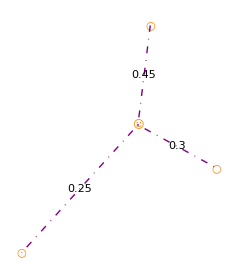

```mathematica
Graphics[{FontSize->44,
barycenter[[1]],
line[[1]],
coeflabel
},
ImageSize->{238,278},AspectRatio->Full]
```

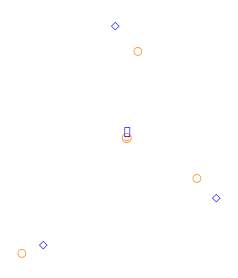

```mathematica
Show[%133,ImageSize->{238,278},AspectRatio->Full]
```